```mathematica
ClearAll["Global`*"];
```

## The Consumer Problem

```mathematica
(*Set parameter values*)
alpha=0.5;(*Preference parameter*)
p1=1;(*Price of good x*)
p2=2;(*Price of good y*)
m=100;(*Income*)
(*Define the utility function*)U[x_,y_]:=x^alpha*y^(1-alpha)
```

```mathematica
(*Define the Lagrangian*)
Lagrangian[x_,y_,lambda_]:=U[x,y]+lambda*(m-p1*x-p2*y)
```

```mathematica
(*Set up the first-order conditions*)
eq1=D[Lagrangian[x,y,lambda],x]==0;
eq2=D[Lagrangian[x,y,lambda],y]==0;
eq3=m-p1*x-p2*y==0;
```

```mathematica
(*Solve the system of equations*)
solution=Solve[{eq1,eq2,eq3},{x,y,lambda}]
```

{{x→50.,y→25.,lambda→0.353553}}

```mathematica
utilityStar=U[x/.solution, y/.solution][[1]];
xStar=x/.solution[[1]];
yStar=y/.solution[[1]];
List[utilityStar,xStar,yStar]
```

{35.3553,50.,25.}

```mathematica
utilityPlot = Plot3D[
U[x,y],{x,0,2*m/p1},{y,0,2*m/p2}
];
optimalBundle3D=Flatten[{xStar,yStar,utilityStar}];
optimalPoint3D[a_]:=
Graphics3D[
{Red,Ball[a,m/(10*(p1+p2))]}
];
```

```mathematica
Show[
utilityPlot,
 optimalPoint3D[optimalBundle3D]
]
```

-Graphics3D-

```mathematica
indiCurves = 
ContourPlot[
U[x,y],{x,0,2*m/p1},{y,0,2*m/p2},
Contours->5,
ContourShading->None,
PlotLegends->Automatic,
FrameLabel->{"good x","good y"},
PlotLabel->"Indifference Curves and Budget Line"
];
```

```mathematica
maxIndiCurve=
ContourPlot[
U[x,y]==utilityStar,
{x,0,2*m/p1},{y,0,2*m/p2},
ContourStyle->Blue
];
```

```mathematica
budget=
Plot[
(m-p1*x)/p2,{x,0,m/p1},
PlotStyle->Directive[Blue,Thick]
];
```

```mathematica
optimalBundle ={xStar,yStar}
```

{50.,25.}

```mathematica
optimalPoint[a_]:=
Graphics[
{Red,PointSize[Large],Point[a]}
];
```

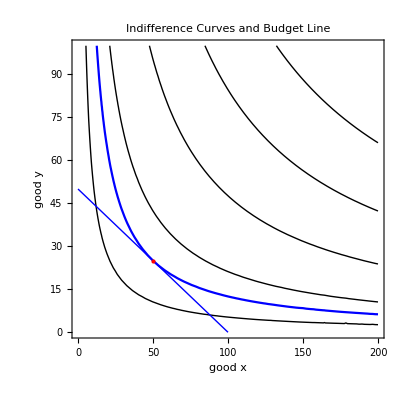

```mathematica
Show[
indiCurves,maxIndiCurve,budget, optimalPoint[optimalBundle]
]
```